# Evaluation of the Dynamic J-integral for the simplified model of the Younan-Veletsos Problem

Joaquin Garcia-Suarez, 2019 (All rights reserved)

This notebook details and displays some results contained in Chapter 5 section 3 and in Appendix D. In particular, the equation that yields the dynamic J-integral is evaluated. In order to generate the plots, as they appear in the text, evaluate this notebook.

## Some integrals that require evaluation

These are just some simple integrals that appear in eq.(4.38) when the approximate displacement field from the reduced model (see section 5.2.3 in the thesis text) is plugged.  The name of the section refers to the coefficients each integral goes with. These integrals are the same that appear in section D.2.4.

The one of C_1^2

```mathematica
FullSimplify[Integrate[r^2*Cos[k*η]^2-c^2*k^2*Sin[k*η]^2,{η,0,1}]]
```

(r^2 (k+Cos[k] Sin[k]))/(2 k)+1/4 c^2 k (-2 k+Sin[2 k])

The one of A^2 (equal minus the one of B^2)

```mathematica
FullSimplify[Integrate[r^2*Cos[r/c*η]^2-r^2*Sin[r/c*η]^2,{η,0,1}]]
```

1/2 c r Sin[(2 r)/c]

The one of 2 AC_1

```mathematica
FullSimplify[Integrate[r^2*Cos[k*η]*Cos[r/c*η]-c*r*k*Sin[k*η]*Sin[r/c*η],{η,0,1}]]
```

c r Cos[k] Sin[r/c]

The one of 2 BC_1

```mathematica
FullSimplify[Integrate[r^2*Cos[k*η]*Sin[r/c*η]+c*r*k*Sin[k*η]*Cos[r/c*η],{η,0,1}]]
```

c r (1-Cos[k] Cos[r/c])

The one of 2BA

```mathematica
2*FullSimplify[Integrate[r^2*Cos[r/c*η]*Sin[r/c*η],{η,0,1}]]
```

c r Sin[r/c]^2

## Auxiliary Parameters

The ration between P and S waves velocities.

```mathematica
c[ν_]:=Sqrt[(2(1-ν))/(1-2ν)]
```

The quasi-static value of κ, whose derivation is much easier (see section D.43), is also included for verification purposes:

```mathematica
κst[ν_]:=c[ν]/Sqrt[(2*c[ν]^2-1)+(672*Catalan*Zeta[3])/π^5(c[ν]^2-1)-(192*Catalan^2)/π^4]
```

It follows finally the term k_n (that serves to consider different modes), as well as the dimensionless frequencies r and r_c (both including the damping).

```mathematica
kn[N_]:=π/2(2N-1)
```

```mathematica
rd[δ_,r_]:=r/Sqrt[1+ⅈ*δ]
```

```mathematica
rc[ν_,δ_,r_]:=(r/c[ν])/Sqrt[1+ⅈ*δ]
```

## Definition of Coefficients

Find next the coefficients that appear in the expression of κ:

```mathematica
un[δ_,r_,N_]:=-2/kn[N] 1/(kn[N]^2-rd[δ,r]^2)
```

```mathematica
CN[ν_,δ_,r_,N_]:=-(c[ν]^2-1)/c[ν]^2 2/((kn[N]^2-rc[ν,δ,r]^2)Sqrt[kn[N]^2-rd[δ,r]^2])
```

```mathematica
AN[ν_,δ_,r_,N_]:=-Sum[CN[ν,δ,r,n],{n,1,N}]
```

```mathematica
BN[ν_,δ_,r_,N_]:=AN[ν,δ,r,N]*Tan[rc[ν,δ,r]]+Sum[(CN[ν,δ,r,n]*kn[n]*(-1)^(n+1))/(rc[ν,δ,r]*Cos[rc[ν,δ,r]])(1-((c[ν]^2-2)/(c[ν]^2-1))*(kn[n]^2-rc[ν,δ,r]^2)/kn[n]^2),{n,1,N}]
```

## Definition of κ

A preliminary note: all the names ending in “N” denote a variable that has to be evaluated as a combination of N modes, where N is the number of modes the user choses (in the thesis case, N=10 was used).

First, consider the right-hand side (RHS) of  eq.(D.80) (which corresponds to the segment in the far-field) once the actual expression of the solution in the far-field, eq.(3.7), has been used in it:

```mathematica
RHSN[ν_,δ_,r_,N_]:=Sum[1/kn[n]^2(1/(kn[n]^2-rd[δ,r]^2)),{n,1,N}]
```

Then, consider the left-hand (LHS) side of the same equation, which takes a more involved form since the displacement field that the model yields due to eq.(D.62) and eq.(D.57). Therefore, an auxiliary function (Aux1) is introduced. Note that the variable LHSN actually is the left-hand side divided by κ^2, that is why later we divide left over right

```mathematica
Aux1N[ν_,δ_,r_,N_]:=-Sin[2*rc[ν,δ,r]]/2(BN[ν,δ,r,N]^2-AN[ν,δ,r,N]^2)+2*BN[ν,δ,r,N]*Sum[CN[ν,δ,r,n],{n,1,N}]+2*AN[ν,δ,r,N]*BN[ν,δ,r,N]*Sin[rc[ν,δ,r]]^2
```

```mathematica
LHSN[ν_,δ_,r_,N_]:=Sum[c[ν]^2/4(kn[n]^2-rd[δ,r]^2)*un[δ,r,n]^2+1/2(-(c[ν]^2 kn[n]^2-rd[δ,r]^2)/2 CN[ν,δ,r,n]^2),{n,1,N}]+1/2(c[ν]*rd[δ,r]*Aux1N[ν,δ,r,N])
```

```mathematica
κdN[ν_,δ_,r_,N_]:=Sqrt[RHSN[ν,δ,r,N]/LHSN[ν,δ,r,N]]
```

## Plots

Compare the dynamic κ to the static κ

Next figure corresponds to Figure 5.7. See that, in the following plots, the variable displayed in the horizontal axis is r, not ω/ω_s=2/π r, as in the actual figure that can be found in the text (to go from one to the other just a trivial re-scaling of the horizontal axis is necessary).

Assign some values to the parameters:

```mathematica
DE=0.05;NU=0.1;
```

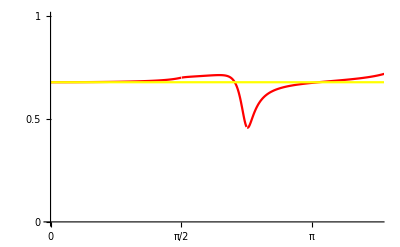

```mathematica
Plot[{Abs[κdN[NU,DE,r,10]],κst[NU]},{r,0,3.5π},PlotRange->{{0,5/4 π},{0,1}},Ticks->{{0,Pi/2, Pi,3 Pi/2},{0,0.5,1}},PlotStyle->{Red,Yellow,Gray}]
```

Plot of the Thrust

Next figure is intended to display at once all the variables depicted in Figure 5.4, one of the most important ones in the text, which contains the exact solution of the thrust as well as the old and the new simplified models. The exact solution can be obtained from evaluating the notebook titled “Chapter4 Exact Solution YV Problem.nb”, whereas all the simplified models are evaluated in the ensuing. First, let us introduce the pieces that conform the thrust. This pieces are missing the effect of κ, which will be added at the end when the actual plot is generated.

## Integral of gradient of horizontal displacement at the wall

```mathematica
intdudxstN[δ_,r_,N_]:=Sum[Sqrt[kn[n]^2-rd[δ,r]^2]/kn[n]*un[δ,r,n],{n,1,N}]
```

## Vertical displacement at the top of the wall

```mathematica
vdynN[ν_,δ_,r_,η_,N_]:=Sum[CN[ν,δ,r,n]*Cos[π/2(2n-1)η],{n,1,N}]+AN[ν,δ,r,N]*Cos[rc[ν,δ,r]*η]+BN[ν,δ,r,N]*Sin[rc[ν,δ,r]*η]
```

## Thrust

Just combining properly these two pieces as eq.(C.33) dictates.

```mathematica
Q[ν_,δ_,r_,N_]:=c[ν]^2*intdudxstN[δ,r,N]+(c[ν]^2-2)*vdynN[ν,δ,r,1,N]
```

## Thrust proposed by Kloukinas et al. (2013)

The expression proposed by Kloukinas and collaborators in their renowned paper is also included. This can be expressed, assuming sinusoidal shape function Φ(η)=sin(π/2 η), as

```mathematica
QKl[ν_,δ_,r_]:=1/Sqrt[(1-ν)(2-ν)](16/π^2)/Sqrt[(π/2)^2-rd[δ,r]^2]
```

## The plot (finally)

The following plot corresponds to Figure 5.4 in the body of the thesis (except for the aforementioned re-scaling of the horizontal axis and the absence of the exact solution, which could be generated by means of the other Mathematica notebook).

Fix the proper values of Poisson’s ratio and damping,

```mathematica
NU=1/3; DE=0.01;
```

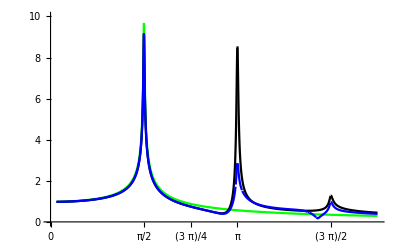

```mathematica
Plot[{Abs[QKl[NU,DE,r]],Abs[κst[NU]*Q[NU,DE,r,10]],Abs[κdN[NU,DE,r,10]*Q[NU,DE,r,10]]},{r,0.1,3.5*π/2},PlotRange->{{0,3.5*π/2},{0,10}},Ticks->{{0,Pi/2,3 Pi/4, Pi,3 Pi/2},{0,1,2,3,4,5,6,7,8,9,10}},PlotStyle->{Green, Black, Blue}]
```

To generate the data presented in Figure 5.5, tweak the value of Poisson’s ratio and damping and re-run the prior Plot function.

Plot of the vertical displacement at the top of the wall

Finally, let us generate the approximations with κ that appear in Figure 5.6. The corresponding values of Poisson’s ratio and damping follow:

```mathematica
NU=0.1; DE=0.05;
```

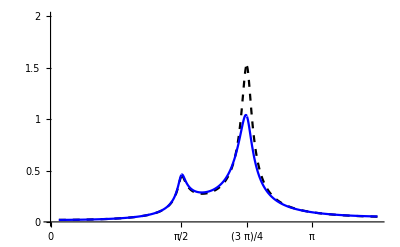

```mathematica
Plot[{Abs[κst[NU]*vdynN[NU,DE,r,1,10]],Abs[κdN[NU,DE,r,10]*vdynN[NU,DE,r,1,10]]},{r,0.1,2.5*π/2},PlotRange->{{0,2.5*π/2},{0,2}},Ticks->{{0,Pi/2,3 Pi/4, Pi,3 Pi/2},{0,0.5,1,1.5,2}},PlotStyle->{{Black,Dashed},Blue}]
```